# PREBIVALSTVO V EVROPI

## UVOZ PODATKOV IZ CSV DATOTEKE IN NEKAJ OSNOV

```mathematica
(*UVOZ PODATKOV*)
data1=Import["europe_population.csv"];
data2=Import["europe_population1.csv"]


(*ZDRUŽEVANJE PODATKOV IZ DVEH DATOTEK*)
data=Join[data1,data2[[2;;3]]];

(*BRISANJE PRAZNIH VRSTIC*)
cleanData=DeleteCases[data,{}];
data=cleanData;

(*PREVERJANJE GLAVE V DATOTEKI IN PARIH VRSTIC*)
header=data[[1]]
values=data[[2;;5]]

(*RAZVRŠČANJE TABELE PO ŠTEVILU PREBIVALCEV*)
sortedBySecondColumn=SortBy[data,#[[2]]&]

(*BRISANJE SPREMENLJIVK header IN values*)
ClearAll[header, values, sortedBySecondColumn]
```

{{Year,Population,Births,Deaths,Natural Change,CBR,CDR,NCR,IMR,TFR,LE},{2020,746225356,6938739,9119281,-2180542,9.3,12.2,-2.9,1.5,1.47,77.7},{2021,745173774,6879818,9656398,-2776580,9.2,13.,-3.7,,1.48,77.}}

{Year,Population,Births,Deaths,Natural Change,CBR,CDR,NCR,IMR,TFR,LE}

{{1951,554559502,12112425,6609794,5502631,21.8,11.9,9.9,-0.8,2.66,62.8},{1952,559609904,12142368,6265135,5877233,21.7,11.2,10.5,-0.8,2.66,64.},{1953,565058633,12120826,6220937,5899889,21.5,11.,10.4,-0.5,2.64,64.7},{1954,570670994,12151779,6072645,6079134,21.3,10.6,10.7,-0.8,2.64,65.5}}

{{1951,554559502,12112425,6609794,5502631,21.8,11.9,9.9,-0.8,2.66,62.8},{1952,559609904,12142368,6265135,5877233,21.7,11.2,10.5,-0.8,2.66,64.},{1953,565058633,12120826,6220937,5899889,21.5,11.,10.4,-0.5,2.64,64.7},{1954,570670994,12151779,6072645,6079134,21.3,10.6,10.7,-0.8,2.64,65.5},{1955,576304974,12134270,5987151,6147119,21.1,10.4,10.7,-0.9,2.63,66.},{1956,581975516,12133583,5899594,6233989,20.8,10.1,10.7,-0.8,2.62,66.9},{1957,587711635,12194100,5963269,6230831,20.7,10.1,10.6,-0.5,2.62,66.9},{1958,593669297,12177600,5647571,6530029,20.5,9.5,11.,-0.9,2.6,68.2},{1959,599684870,12178245,5816056,6362189,20.3,9.7,10.6,-0.7,2.6,68.1},{1960,605629870,12098378,5783828,6314550,20.,9.6,10.4,-0.4,2.58,68.8},{1961,611711020,11990399,5749292,6241107,19.6,9.4,10.2,-0.5,2.56,69.1},{1962,617672206,11784056,6023706,5760350,19.1,9.8,9.3,-0.1,2.53,68.9},{1963,623335994,11654646,6031219,5623427,18.7,9.7,9.,0,2.52,69.2},{1964,628944878,11467618,5843514,5624104,18.2,9.3,8.9,-0.4,2.5,69.9},{1965,634267606,11141596,6058752,5082844,17.6,9.6,8.,-0.1,2.45,69.8},{1966,639264461,10950076,6074808,4875268,17.1,9.5,7.6,0,2.42,70.},{1967,644114436,10969039,6204646,4764393,17.,9.6,7.4,-0.4,2.42,70.},{1968,648610191,10821004,6427622,4393382,16.7,9.9,6.8,-0.4,2.38,69.9},{1969,652740596,10685498,6652543,4032955,16.4,10.2,6.2,-0.4,2.33,69.6},{1970,656521426,10568071,6602177,3965894,16.1,10.1,6.,0,2.28,70.},{1971,660476010,10662541,6675051,3987490,16.1,10.1,6.,0.5,2.27,70.1},{1972,664799679,10499844,6699913,3799931,15.8,10.1,5.7,0.5,2.21,70.3},{1973,668909022,10322172,6814598,3507574,15.4,10.2,5.2,0.8,2.14,70.4},{1974,672912941,10406013,6818259,3587754,15.5,10.1,5.3,0.4,2.13,70.6},{1975,676770845,10285047,7009188,3275859,15.2,10.4,4.8,0.5,2.07,70.5},{1976,680361150,10242399,7085837,3156562,15.1,10.4,4.6,0.5,2.03,70.6},{1977,683848710,10171264,7039667,3131597,14.9,10.3,4.6,0.2,1.99,70.9},{1978,687149553,10143418,7183531,2959887,14.8,10.5,4.3,0.3,1.96,70.9},{1979,690287705,10159933,7268744,2891189,14.7,10.5,4.2,0.4,1.95,71.},{1980,693437228,10156371,7422720,2733651,14.6,10.7,3.9,0.4,1.93,70.9},{1981,696429190,10053030,7404116,2648914,14.4,10.6,3.8,0.2,1.89,71.2},{1982,699220370,10102647,7373734,2728913,14.4,10.5,3.9,0.1,1.89,71.5},{1983,702014774,10078184,7562097,2516087,14.4,10.8,3.6,0.4,1.87,71.5},{1984,704798623,10050688,7584914,2465774,14.3,10.8,3.5,0.4,1.86,71.6},{1985,707516287,9969920,7702883,2267037,14.1,10.9,3.2,0.9,1.84,71.7},{1986,710385076,9987274,7423641,2563633,14.1,10.5,3.6,0.7,1.84,72.5},{1987,713465338,9966304,7407417,2558887,14.,10.4,3.6,0.6,1.84,72.7},{1988,716444431,9840567,7475880,2364687,13.7,10.4,3.3,0.4,1.82,72.8},{1989,719107883,9495117,7527904,1967213,13.2,10.5,2.7,0.6,1.76,72.9},{1990,721497282,9235425,7681197,1554228,12.8,10.6,2.2,0.7,1.72,72.9},{1991,723602898,8888909,7796555,1092354,12.3,10.8,1.5,0.8,1.66,72.9},{1992,725259493,8523515,7935829,587686,11.8,10.9,0.8,0.8,1.6,72.7},{1993,726441892,8138793,8412609,-273816,11.2,11.6,-0.4,1.4,1.53,72.1},{2001,726878371,7277594,8364598,-1087004,10.,11.5,-1.5,1.6,1.41,73.8},{2002,726939358,7330526,8520890,-1190364,10.1,11.7,-1.6,2.3,1.42,73.8},{2000,726968473,7325763,8401888,-1076125,10.1,11.6,-1.5,1.4,1.42,73.5},{1994,727063162,7913453,8492472,-579019,10.9,11.7,-0.8,1.1,1.5,72.1},{1999,727100016,7264382,8402774,-1138392,10.,11.6,-1.6,1.4,1.4,73.4},{1995,727300408,7663831,8553348,-889517,10.5,11.8,-1.2,1.4,1.46,72.2},{2003,727424988,7442475,8655471,-1212996,10.2,11.9,-1.7,2.7,1.45,73.8},{1998,727445606,7369527,8193143,-823616,10.1,11.3,-1.1,0.6,1.42,73.6},{1996,727453566,7581575,8394631,-813056,10.4,11.5,-1.1,1.3,1.45,72.7},{1997,727566480,7476674,8240385,-763711,10.3,11.3,-1.,0.8,1.43,73.2},{2004,728163243,7558652,8381363,-822711,10.4,11.5,-1.1,2.2,1.47,74.4},{2005,728950486,7568637,8494391,-925754,10.4,11.7,-1.3,2.5,1.47,74.5},{2006,729857708,7703029,8237212,-534183,10.6,11.3,-0.7,2.8,1.5,75.2},{2007,731393136,7886129,8187820,-301691,10.8,11.2,-0.4,2.9,1.54,75.6},{2008,733256182,8169398,8195293,-25895,11.1,11.2,0.,2.2,1.59,75.8},{2009,734902805,8208268,8099043,109225,11.2,11.,0.1,1.8,1.6,76.3},{2010,736276813,8227484,8128387,99097,11.2,11.,0.1,1.7,1.61,76.5},{2011,737589666,8132980,7958960,174020,11.,10.8,0.2,1.6,1.6,77.1},{2012,738907594,8178804,8078292,100512,11.1,10.9,0.1,1.4,1.62,77.3},{2013,740013806,8039791,8033963,5828,10.9,10.9,0.,1.4,1.6,77.6},{2014,741014147,8067454,7955740,111714,10.9,10.7,0.2,1.3,1.62,77.9},{2015,742107449,8004465,8177599,-173134,10.8,11.,-0.2,1.8,1.62,78.},{2016,743318582,7950684,8009194,-58510,10.7,10.8,-0.1,1.6,1.62,78.4},{2017,744449361,7617755,8076159,-458404,10.2,10.8,-0.6,1.8,1.56,78.7},{2021,745173774,6879818,9656398,-2776580,9.2,13.,-3.7,,1.48,77.},{2018,745359130,7375157,8112356,-737199,9.9,10.9,-1.,2.1,1.53,78.8},{2019,746189645,7108392,8020246,-911854,9.5,10.7,-1.2,1.2,1.49,79.1},{2020,746225356,6938739,9119281,-2180542,9.3,12.2,-2.9,1.5,1.47,77.7},{Year,Population,Births,Deaths,Natural Change,CBR,CDR,NCR,IMR,TFR,LE}}

## RAZVRSTITEV PODATKOV IN OSNOVNE FUNKCIJE

```mathematica
(*RAZVRSTITEV PODATKOV V POSAMEZNE SEZNAME*)
yearList=data[[2;;,1]];
populationList=data[[2;;,2]];
birthsList=data[[2;;,3]];
deathsList=data[[2;;,4]];
naturalChangeList=data[[2;;,5]];
cbrList=data[[2;;,6]];
cdrList=data[[2;;,7]];
ncrList=data[[2;;,8]];
imrList=data[[2;;,9]];
tfrList=data[[2;;,10]];
```

```mathematica
(*LETO Z NAJMANJ IN NAJVEČ PREBIVALCI*)
letoMinPrebivalcev=yearList[[First[Ordering[populationList,1]]]];
letoMaxPrebivalcev=yearList[[First[Ordering[populationList,-1]]]];

(*LETO Z NAJMANJŠIM IN NAJVEČJIM ŠTEVILOM ROJSTEV*)
letoMinRojstev=yearList[[First[Ordering[birthsList,1]]]];
letoMaxRojstev=yearList[[First[Ordering[birthsList,-1]]]];

(*LETO Z NAJMANJŠIM IN NAJVEČJIM ŠTEVILOM SMRTI*)
letoMinSmrti=yearList[[First[Ordering[deathsList,1]]]];
letoMaxSmrti=yearList[[First[Ordering[deathsList,-1]]]];

(*IZPISANO NAJVIŠJE IN NAJNIŽJE ŠTEVILO POPULACIJE TER IZRAČUNANE POVPREČNE VREDNOSTI POPULACIJE, RODNOSTI IN UMRLJIVOSTI.*)
maxPopulation=Max[populationList];
minPopulation=Min[populationList];
avgPopulation=N[Mean[populationList]];
avgBirths=Ceiling[Mean[birthsList]];
avgDeaths=Floor[Mean[deathsList]];

(*IZRAČUNANA SREDNJA VREDNOST IN STANDARDNI ODKLON PREBIVALSTVA TER NAJVEČJA RAZLIKA MED RODNJOSTJO IN UMRLJIVOSTJO.*)
medianPopulation=Median[populationList]
stdDevPopulation=Floor[StandardDeviation[populationList]]
maxDifference=Max[Abs[Subtract[deathsList,birthsList]]]

Print["Največ prebivalcev je Evropa štela leta ", letoMaxPrebivalcev ,", kar ", maxPopulation, ","," najmanj pa ", letoMinPrebivalcev, " in sicer ",minPopulation, ". Največ otrok se je rodilo leta ", letoMaxRojstev,", medtem ko jih je leta " ,letoMinRojstev," bilo najmanj. Leta ", letoMinSmrti, " je bilo v Evropi najmanj smrti, medtem ko jih je bilo leta " ,letoMaxSmrti ," največ."]

Print["Povprečna vrednost populacije je ",avgPopulation, ","," medtem ko je povprečje rodnosti ", avgBirths, " ter smrtnosti ", avgDeaths, "."]
```

710385076

56449184

6530029

Največ prebivalcev je Evropa štela leta 2020, kar 746225356, najmanj pa 1951 in sicer 554559502. Največ otrok se je rodilo leta 1957, medtem ko jih je leta 2021 bilo najmanj. Leta 1958 je bilo v Evropi najmanj smrti, medtem ko jih je bilo leta 2021 največ.

Povprečna vrednost populacije je 6.86796×10^8, medtem ko je povprečje rodnosti 9508682 ter smrtnosti 7385659.

## VIZUALIZACIJA PODATKOV

```mathematica
(*PREDSTAVITEV PODATKOV V TABELI*)
dataTable=Transpose[{yearList,populationList,birthsList,deathsList,naturalChangeList,cbrList,cdrList,ncrList,imrList,tfrList}];
TableForm[dataTable,TableHeadings->{None,{"Leto","Prebivalstvo","Rojstva","Smrti","Naravna sprememba","Stopnja rojstev (CBR)","Stopnja smrti (CDR)","Naravna sprememba (NCR)","Umrljivost novorojenčkov (IMR)","Skupna rodnost (TFR)"}}]
```

Leto | Prebivalstvo | Rojstva | Smrti | Naravna sprememba | Stopnja rojstev (CBR) | Stopnja smrti (CDR) | Naravna sprememba (NCR) | Umrljivost novorojenčkov (IMR) | Skupna rodnost (TFR)
1951 | 554559502 | 12112425 | 6609794 | 5502631 | 21.8 | 11.9 | 9.9 | -0.8 | 2.66
1952 | 559609904 | 12142368 | 6265135 | 5877233 | 21.7 | 11.2 | 10.5 | -0.8 | 2.66
1953 | 565058633 | 12120826 | 6220937 | 5899889 | 21.5 | 11. | 10.4 | -0.5 | 2.64
1954 | 570670994 | 12151779 | 6072645 | 6079134 | 21.3 | 10.6 | 10.7 | -0.8 | 2.64
1955 | 576304974 | 12134270 | 5987151 | 6147119 | 21.1 | 10.4 | 10.7 | -0.9 | 2.63
1956 | 581975516 | 12133583 | 5899594 | 6233989 | 20.8 | 10.1 | 10.7 | -0.8 | 2.62
1957 | 587711635 | 12194100 | 5963269 | 6230831 | 20.7 | 10.1 | 10.6 | -0.5 | 2.62
1958 | 593669297 | 12177600 | 5647571 | 6530029 | 20.5 | 9.5 | 11. | -0.9 | 2.6
1959 | 599684870 | 12178245 | 5816056 | 6362189 | 20.3 | 9.7 | 10.6 | -0.7 | 2.6
1960 | 605629870 | 12098378 | 5783828 | 6314550 | 20. | 9.6 | 10.4 | -0.4 | 2.58
1961 | 611711020 | 11990399 | 5749292 | 6241107 | 19.6 | 9.4 | 10.2 | -0.5 | 2.56
1962 | 617672206 | 11784056 | 6023706 | 5760350 | 19.1 | 9.8 | 9.3 | -0.1 | 2.53
1963 | 623335994 | 11654646 | 6031219 | 5623427 | 18.7 | 9.7 | 9. | 0 | 2.52
1964 | 628944878 | 11467618 | 5843514 | 5624104 | 18.2 | 9.3 | 8.9 | -0.4 | 2.5
1965 | 634267606 | 11141596 | 6058752 | 5082844 | 17.6 | 9.6 | 8. | -0.1 | 2.45
1966 | 639264461 | 10950076 | 6074808 | 4875268 | 17.1 | 9.5 | 7.6 | 0 | 2.42
1967 | 644114436 | 10969039 | 6204646 | 4764393 | 17. | 9.6 | 7.4 | -0.4 | 2.42
1968 | 648610191 | 10821004 | 6427622 | 4393382 | 16.7 | 9.9 | 6.8 | -0.4 | 2.38
1969 | 652740596 | 10685498 | 6652543 | 4032955 | 16.4 | 10.2 | 6.2 | -0.4 | 2.33
1970 | 656521426 | 10568071 | 6602177 | 3965894 | 16.1 | 10.1 | 6. | 0 | 2.28
1971 | 660476010 | 10662541 | 6675051 | 3987490 | 16.1 | 10.1 | 6. | 0.5 | 2.27
1972 | 664799679 | 10499844 | 6699913 | 3799931 | 15.8 | 10.1 | 5.7 | 0.5 | 2.21
1973 | 668909022 | 10322172 | 6814598 | 3507574 | 15.4 | 10.2 | 5.2 | 0.8 | 2.14
1974 | 672912941 | 10406013 | 6818259 | 3587754 | 15.5 | 10.1 | 5.3 | 0.4 | 2.13
1975 | 676770845 | 10285047 | 7009188 | 3275859 | 15.2 | 10.4 | 4.8 | 0.5 | 2.07
1976 | 680361150 | 10242399 | 7085837 | 3156562 | 15.1 | 10.4 | 4.6 | 0.5 | 2.03
1977 | 683848710 | 10171264 | 7039667 | 3131597 | 14.9 | 10.3 | 4.6 | 0.2 | 1.99
1978 | 687149553 | 10143418 | 7183531 | 2959887 | 14.8 | 10.5 | 4.3 | 0.3 | 1.96
1979 | 690287705 | 10159933 | 7268744 | 2891189 | 14.7 | 10.5 | 4.2 | 0.4 | 1.95
1980 | 693437228 | 10156371 | 7422720 | 2733651 | 14.6 | 10.7 | 3.9 | 0.4 | 1.93
1981 | 696429190 | 10053030 | 7404116 | 2648914 | 14.4 | 10.6 | 3.8 | 0.2 | 1.89
1982 | 699220370 | 10102647 | 7373734 | 2728913 | 14.4 | 10.5 | 3.9 | 0.1 | 1.89
1983 | 702014774 | 10078184 | 7562097 | 2516087 | 14.4 | 10.8 | 3.6 | 0.4 | 1.87
1984 | 704798623 | 10050688 | 7584914 | 2465774 | 14.3 | 10.8 | 3.5 | 0.4 | 1.86
1985 | 707516287 | 9969920 | 7702883 | 2267037 | 14.1 | 10.9 | 3.2 | 0.9 | 1.84
1986 | 710385076 | 9987274 | 7423641 | 2563633 | 14.1 | 10.5 | 3.6 | 0.7 | 1.84
1987 | 713465338 | 9966304 | 7407417 | 2558887 | 14. | 10.4 | 3.6 | 0.6 | 1.84
1988 | 716444431 | 9840567 | 7475880 | 2364687 | 13.7 | 10.4 | 3.3 | 0.4 | 1.82
1989 | 719107883 | 9495117 | 7527904 | 1967213 | 13.2 | 10.5 | 2.7 | 0.6 | 1.76
1990 | 721497282 | 9235425 | 7681197 | 1554228 | 12.8 | 10.6 | 2.2 | 0.7 | 1.72
1991 | 723602898 | 8888909 | 7796555 | 1092354 | 12.3 | 10.8 | 1.5 | 0.8 | 1.66
1992 | 725259493 | 8523515 | 7935829 | 587686 | 11.8 | 10.9 | 0.8 | 0.8 | 1.6
1993 | 726441892 | 8138793 | 8412609 | -273816 | 11.2 | 11.6 | -0.4 | 1.4 | 1.53
1994 | 727063162 | 7913453 | 8492472 | -579019 | 10.9 | 11.7 | -0.8 | 1.1 | 1.5
1995 | 727300408 | 7663831 | 8553348 | -889517 | 10.5 | 11.8 | -1.2 | 1.4 | 1.46
1996 | 727453566 | 7581575 | 8394631 | -813056 | 10.4 | 11.5 | -1.1 | 1.3 | 1.45
1997 | 727566480 | 7476674 | 8240385 | -763711 | 10.3 | 11.3 | -1. | 0.8 | 1.43
1998 | 727445606 | 7369527 | 8193143 | -823616 | 10.1 | 11.3 | -1.1 | 0.6 | 1.42
1999 | 727100016 | 7264382 | 8402774 | -1138392 | 10. | 11.6 | -1.6 | 1.4 | 1.4
2000 | 726968473 | 7325763 | 8401888 | -1076125 | 10.1 | 11.6 | -1.5 | 1.4 | 1.42
2001 | 726878371 | 7277594 | 8364598 | -1087004 | 10. | 11.5 | -1.5 | 1.6 | 1.41
2002 | 726939358 | 7330526 | 8520890 | -1190364 | 10.1 | 11.7 | -1.6 | 2.3 | 1.42
2003 | 727424988 | 7442475 | 8655471 | -1212996 | 10.2 | 11.9 | -1.7 | 2.7 | 1.45
2004 | 728163243 | 7558652 | 8381363 | -822711 | 10.4 | 11.5 | -1.1 | 2.2 | 1.47
2005 | 728950486 | 7568637 | 8494391 | -925754 | 10.4 | 11.7 | -1.3 | 2.5 | 1.47
2006 | 729857708 | 7703029 | 8237212 | -534183 | 10.6 | 11.3 | -0.7 | 2.8 | 1.5
2007 | 731393136 | 7886129 | 8187820 | -301691 | 10.8 | 11.2 | -0.4 | 2.9 | 1.54
2008 | 733256182 | 8169398 | 8195293 | -25895 | 11.1 | 11.2 | 0. | 2.2 | 1.59
2009 | 734902805 | 8208268 | 8099043 | 109225 | 11.2 | 11. | 0.1 | 1.8 | 1.6
2010 | 736276813 | 8227484 | 8128387 | 99097 | 11.2 | 11. | 0.1 | 1.7 | 1.61
2011 | 737589666 | 8132980 | 7958960 | 174020 | 11. | 10.8 | 0.2 | 1.6 | 1.6
2012 | 738907594 | 8178804 | 8078292 | 100512 | 11.1 | 10.9 | 0.1 | 1.4 | 1.62
2013 | 740013806 | 8039791 | 8033963 | 5828 | 10.9 | 10.9 | 0. | 1.4 | 1.6
2014 | 741014147 | 8067454 | 7955740 | 111714 | 10.9 | 10.7 | 0.2 | 1.3 | 1.62
2015 | 742107449 | 8004465 | 8177599 | -173134 | 10.8 | 11. | -0.2 | 1.8 | 1.62
2016 | 743318582 | 7950684 | 8009194 | -58510 | 10.7 | 10.8 | -0.1 | 1.6 | 1.62
2017 | 744449361 | 7617755 | 8076159 | -458404 | 10.2 | 10.8 | -0.6 | 1.8 | 1.56
2018 | 745359130 | 7375157 | 8112356 | -737199 | 9.9 | 10.9 | -1. | 2.1 | 1.53
2019 | 746189645 | 7108392 | 8020246 | -911854 | 9.5 | 10.7 | -1.2 | 1.2 | 1.49
2020 | 746225356 | 6938739 | 9119281 | -2180542 | 9.3 | 12.2 | -2.9 | 1.5 | 1.47
2021 | 745173774 | 6879818 | 9656398 | -2776580 | 9.2 | 13. | -3.7 |  | 1.48

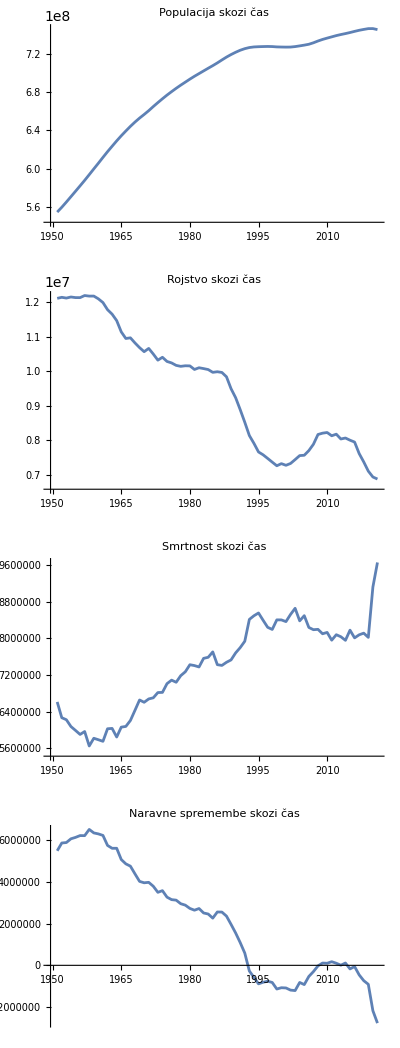

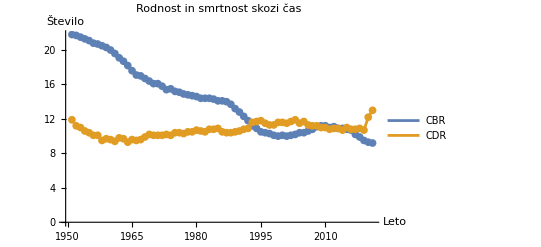

-Graphics3D-

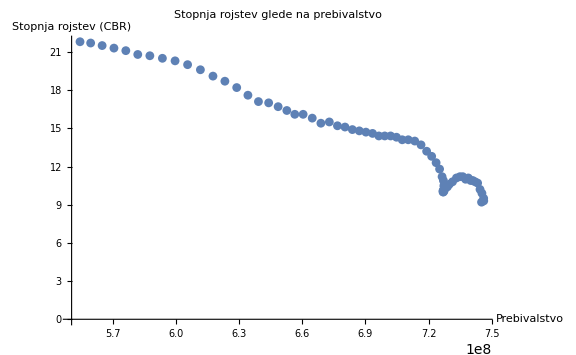

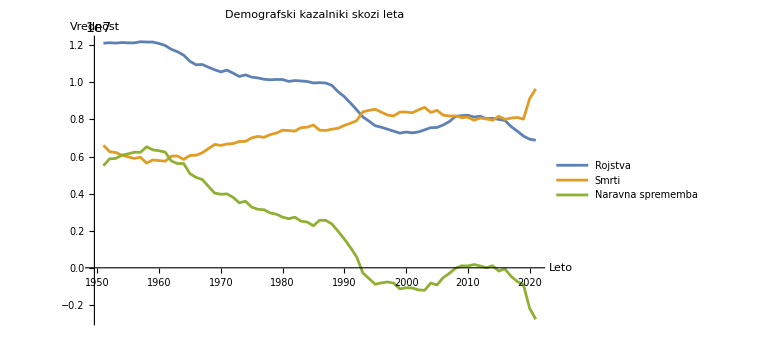

```mathematica
(*GRAF PRIKAZUJE SPREMINJANJE ŠTEVILA PREBIVALSTVA, ROJSTEV, SMRTI IN NARAVNIH SPREMEMB*)
GraphicsGrid[{{ListLinePlot[Transpose[{yearList,populationList}],PlotLabel->"Populacija skozi čas"]},{ListLinePlot[Transpose[{yearList,birthsList}],PlotLabel->"Rojstvo skozi čas"]},{ListLinePlot[Transpose[{yearList,deathsList}],PlotLabel->"Smrtnost skozi čas"]},{ListLinePlot[Transpose[{yearList,naturalChangeList}],PlotLabel->"Naravne spremembe skozi čas"]}}]

(*GRAF RODNOSTI IN SMRTNOSTI*)
ListLinePlot[{Transpose[{yearList,cbrList}],Transpose[{yearList,cdrList}]},PlotLegends->{"CBR","CDR"},AxesLabel->{"Leto","Število"},PlotLabel->"Rodnost in smrtnost skozi čas",Mesh->All]

(*GRAF PRIKAZUJE POVEZAVO MED STOPNJO ROJSTEV IN ŠTEVILOM SMRTI.*)
ListPointPlot3D[Transpose[{birthsList,yearList,deathsList}],PlotStyle->Red,AxesLabel->{"Stopnja rojstev","Leto","Število smrti"},PlotLabel->"Število smrti glede na stopnjo rojstev in smrti glede na leto",PlotRange->{{6000000,12000000},All,{6000000,10000000}},Boxed->True,AspectRatio->Automatic,ImageSize->Large  ]

(*GRAF STOPNJE ROJSTVA V PRIMERJAVI Z PREBIVALSTOM*)
ListPlot[Transpose[{populationList,cbrList}],AxesLabel->{"Prebivalstvo","Stopnja rojstev (CBR)"},PlotLabel->"Stopnja rojstev glede na prebivalstvo",ImageSize->Large]

(*GRAF PRIKAZUJE RODNOST, UMRLJIVOST IN NARAVNO SPREMEMBO SKOZI LETA*)
ListLinePlot[{Transpose[{yearList,birthsList}],Transpose[{yearList,deathsList}],Transpose[{yearList,naturalChangeList}]},PlotLabel->"Demografski kazalniki skozi leta",PlotLegends->{"Rojstva","Smrti","Naravna sprememba"},AxesLabel->{"Leto","Vrednost"},ImageSize->Large]
```

## FUNKCIJE

2.33824×10^6

{1958,6530029/593669297}

{1958,5957662/587711635}

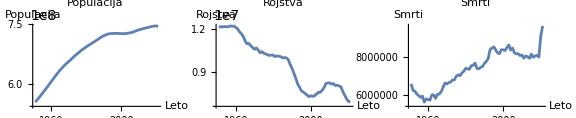

```mathematica
(*Izračunava ponderirano povprečno rast prebivalstva.*)
weightedAverageGrowthRate[population_List,changes_List]:=Module[{weights,weightedGrowthRates},weights=N[Map[1/#&,population]];(*Pretvori populacijo v decimalne*)weightedGrowthRates=MapThread[#1*#2&,{weights,changes}];(*Ponderirana rast*)Total[weightedGrowthRates]/Total[weights]  (*Izračun povprečne rasti*)]

avgWeightedGrowth=weightedAverageGrowthRate[populationList,naturalChangeList]

(*Poišče leto z največjim naravnim povečanjem na prebivalca.*)
maxNaturalChangePerCapita[years_List,changes_List,population_List]:=Module[{perCapita,maxIndex},perCapita=MapThread[#1/#2&,{changes,population}];
maxIndex=First[Ordering[perCapita,-1]];
{years[[maxIndex]],perCapita[[maxIndex]]}]

maxChangeYear=maxNaturalChangePerCapita[yearList,naturalChangeList,populationList]

(*Uporablja se za iskanje let z najvišjo in najnižjo smrtnostjo.*)
(*Ustvarimo dataset z letnicami in smrtnostjo*)dataset=Dataset[Transpose[{yearList,cdrList}]];
maxMortalityYear=dataset[Query[MaximalBy[Last]]]
minMortalityYear=dataset[Query[MinimalBy[Last]]]

(*Najde leto z največjo rastjo populacije.*)
yearOfMaxPopulationGrowth[years_List,population_List]:=Module[{growthRates,maxIndex},growthRates=Differences[population]/Most[population];
maxIndex=First[Ordering[growthRates,-1]];
{years[[maxIndex+1]],growthRates[[maxIndex]]}]

maxGrowthYear=yearOfMaxPopulationGrowth[yearList,populationList]

(*Ustvarjanje grafov s seznami podatkov*)plots=MapThread[ListLinePlot[#1,PlotLabel->#2,AxesLabel->{"Leto",#2}]&,{{Transpose[{yearList,populationList}],Transpose[{yearList,birthsList}],Transpose[{yearList,deathsList}]},{"Populacija","Rojstva","Smrti"}}];

(*Prikaz vseh treh grafov v eni vrstici*)GraphicsGrid[{plots},Spacings->{2,1},ImageSize->Large]
```

```mathematica
(*Filtrirajte podatke med leti 2000 in 2010*)filteredData=Select[data,#[[1]]>=2000&&#[[1]]<=2010&]

(*Definirajte dva seznama*)years=data[[2;;,1]];
populations=data[[2;;,2]];

(*Uporabite MapThread za ustvarjanje seznama parov*)
yearPopulationPairs=MapThread[List,{years,populations}]

(*Definirajte funkcijo*)
razlikaRojstvaSmrti[x_,y_]:=x-y

(*Uporabite Apply za uporabo funkcije na seznamu*)
result=Apply[razlikaRojstvaSmrti,{births,deaths}]

(*Funkcija za izračun povprečne populacije med leti*)averagePopulation[yearRange_]:=Module[{filtered,populations},filtered=Select[data,MemberQ[yearRange,#[[1]]]&];
populations=filtered[[All,2]];
Mean[populations]]

(*Uporabite funkcijo za izračun povprečne populacije med leti 2000 in 2009*)
averagePopulation[Range[2000,2009]]
```

{{2000,726968473,7325763,8401888,-1076125,10.1,11.6,-1.5,1.4,1.42,73.5},{2001,726878371,7277594,8364598,-1087004,10.,11.5,-1.5,1.6,1.41,73.8},{2002,726939358,7330526,8520890,-1190364,10.1,11.7,-1.6,2.3,1.42,73.8},{2003,727424988,7442475,8655471,-1212996,10.2,11.9,-1.7,2.7,1.45,73.8},{2004,728163243,7558652,8381363,-822711,10.4,11.5,-1.1,2.2,1.47,74.4},{2005,728950486,7568637,8494391,-925754,10.4,11.7,-1.3,2.5,1.47,74.5},{2006,729857708,7703029,8237212,-534183,10.6,11.3,-0.7,2.8,1.5,75.2},{2007,731393136,7886129,8187820,-301691,10.8,11.2,-0.4,2.9,1.54,75.6},{2008,733256182,8169398,8195293,-25895,11.1,11.2,0.,2.2,1.59,75.8},{2009,734902805,8208268,8099043,109225,11.2,11.,0.1,1.8,1.6,76.3},{2010,736276813,8227484,8128387,99097,11.2,11.,0.1,1.7,1.61,76.5}}

{{1951,554559502},{1952,559609904},{1953,565058633},{1954,570670994},{1955,576304974},{1956,581975516},{1957,587711635},{1958,593669297},{1959,599684870},{1960,605629870},{1961,611711020},{1962,617672206},{1963,623335994},{1964,628944878},{1965,634267606},{1966,639264461},{1967,644114436},{1968,648610191},{1969,652740596},{1970,656521426},{1971,660476010},{1972,664799679},{1973,668909022},{1974,672912941},{1975,676770845},{1976,680361150},{1977,683848710},{1978,687149553},{1979,690287705},{1980,693437228},{1981,696429190},{1982,699220370},{1983,702014774},{1984,704798623},{1985,707516287},{1986,710385076},{1987,713465338},{1988,716444431},{1989,719107883},{1990,721497282},{1991,723602898},{1992,725259493},{1993,726441892},{1994,727063162},{1995,727300408},{1996,727453566},{1997,727566480},{1998,727445606},{1999,727100016},{2000,726968473},{2001,726878371},{2002,726939358},{2003,727424988},{2004,728163243},{2005,728950486},{2006,729857708},{2007,731393136},{2008,733256182},{2009,734902805},{2010,736276813},{2011,737589666},{2012,738907594},{2013,740013806},{2014,741014147},{2015,742107449},{2016,743318582},{2017,744449361},{2018,745359130},{2019,746189645},{2020,746225356},{2021,745173774}}

{5502631,5877233,5899889,6079134,6147119,6233989,6230831,6530029,6362189,6314550,6241107,5760350,5623427,5624104,5082844,4875268,4764393,4393382,4032955,3965894,3987490,3799931,3507574,3587754,3275859,3156562,3131597,2959887,2891189,2733651,2648914,2728913,2516087,2465774,2267037,2563633,2558887,2364687,1967213,1554228,1092354,587686,-273816,-579019,-889517,-813056,-763711,-823616,-1138392,-1076125,-1087004,-1190364,-1212996,-822711,-925754,-534183,-301691,-25895,109225,99097,174020,100512,5828,111714,-173134,-58510,-458404,-737199,-911854,-2180542,-2776580}

729473475

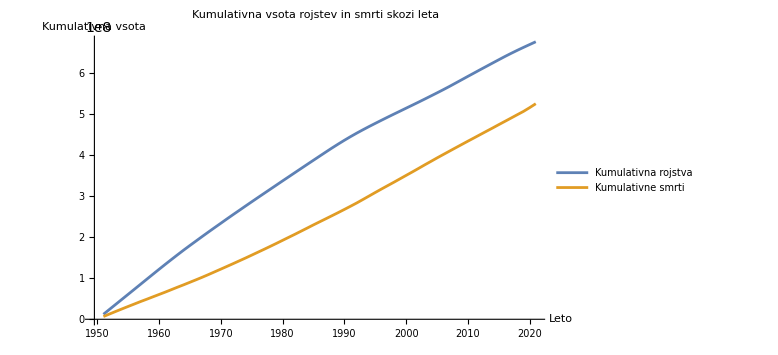

```mathematica
(*Izračuna kumulativno število rojstev in smrti.*)cumulativeData[data_List]:=FoldList[Plus,First[data],Rest[data]]

cumulativeBirths=cumulativeData[birthsList];
cumulativeDeaths=cumulativeData[deathsList];

(*Ustvari seznama z leti in kumulativnimi podatki za graf.*)
cumulativeBirthsWithYears=Transpose[{yearList,cumulativeBirths}];
cumulativeDeathsWithYears=Transpose[{yearList,cumulativeDeaths}];

(*Prikaz kumulativnih rojstev in smrti s pripadajočimi leti.*)
ListLinePlot[{cumulativeBirthsWithYears,cumulativeDeathsWithYears},PlotLegends->{"Kumulativna rojstva","Kumulativne smrti"},AxesLabel->{"Leto","Kumulativna vsota"},PlotLabel->"Kumulativna vsota rojstev in smrti skozi leta",ImageSize->Large]
```

## MALO PRIHODNOSTI

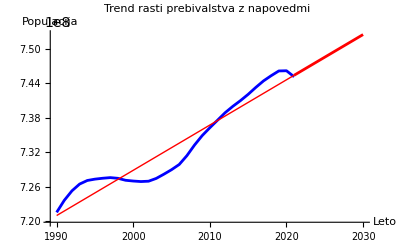

{7.45436×10^8,7.46226×10^8,7.47016×10^8,7.47806×10^8,7.48596×10^8,7.49386×10^8,7.50176×10^8,7.50966×10^8,7.51756×10^8,7.52546×10^8}

```mathematica
(*Funkcija za analizo trendov rasti prebivalstva*)(*Določite zadnjih 20 let*)recentYears=Select[yearList,#>=1990&];
recentPopulations=Select[Transpose[{yearList,populationList}],#[[1]]>=1990&][[All,2]];

(*Ustvari napoved za prihodnja leta*)
futureYears=Range[2021,2030]; (*Napovedujemo za prihodnja leta*)

(*Funkcija za analizo trendov rasti prebivalstva*)
analyzePopulationTrends[years_,populations_,futureYears_]:=Module[{model,futurePredictions,trendPlot},(*Prilagodimo linearni model*)model=Fit[Transpose[{years,populations}],{1,x},x];
(*Izračunamo napovedane vrednosti za prihodnja leta*)futurePredictions=model/. x->futureYears;
(*Ustvarimo graf rasti prebivalstva z modelom*)trendPlot=ListLinePlot[{Transpose[{years,populations}],Transpose[{futureYears,futurePredictions}]},PlotStyle->{Blue,Red},(*Modra za dejanske podatke,rdeča za napoved*)PlotRange->{All,All},(*Prikazuje vse podatke*)AxesLabel->{"Leto","Populacija"},PlotLabel->"Trend rasti prebivalstva z napovedmi",Epilog->{Red,Line[Transpose[{years,model/. x->years}]]}];
(*Vrnemo graf in napovedane vrednosti*){trendPlot,futurePredictions}];

(*Uporaba funkcije za zadnjih 20 let*)
{trendPlot,futurePredictions}=analyzePopulationTrends[recentYears,recentPopulations,futureYears];

(*Prikaz grafov*)
trendPlot
futurePredictions
```

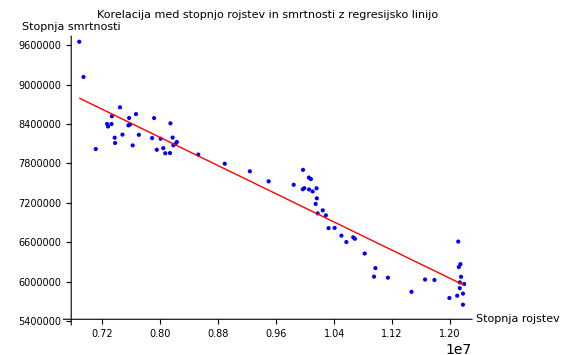

```mathematica
(*Funkcija za analizo korelacije in prikaz linearne regresije*)correlationWithRegressionPlot[births_,deaths_,years_]:=Module[{data,regressionLine,plot},(*Priprava podatkov*)data=Transpose[{births,deaths}];
(*Izračun linearne regresije*)regressionLine=Fit[data,{1,x},x];
(*Ustvarimo graf za prikaz korelacije in regresijske linije*)plot=ListPlot[data,PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"Stopnja rojstev","Stopnja smrtnosti"},PlotLabel->"Korelacija med stopnjo rojstev in smrtnosti z regresijsko linijo",ImageSize->Large,Epilog->{Red,Line[{{Min[births],regressionLine/. x->Min[births]},{Max[births],regressionLine/. x->Max[births]}}]}];
(*Vrnemo graf*)plot];

(*Uporaba funkcije*)
correlationWithRegressionPlot[birthsList,deathsList,yearList]
```

```mathematica
(*IZVOZI GRAF PREBIVALSTVO SKOZI LETA V prebivalstvo_graf.png IN PODATKE V podatki_tabela.csv*)
Export["podatki_tabela.csv",dataTable];
Export["prebivalstvo_graf.png",ListLinePlot[Transpose[{yearList,populationList}],AxesLabel->{"Leto","Prebivalstvo"},PlotLabel->"Prebivalstvo skozi leta",PlotTheme->"Detailed",ImageSize->Large]];
```